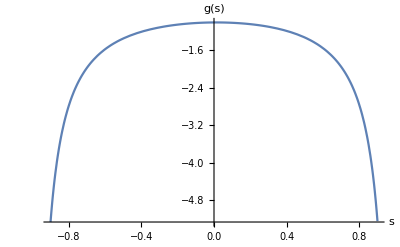

```mathematica
ClearAll[g,λ];
n=200;(*Number of Gauss points*)λ=1;(*eigenvalue*)
{pts,w}=Most[NIntegrate`GaussRuleData[n,MachinePrecision]];

(*Map interval from[-1,1] to general interval*)
sList=Rescale[pts,{0,1},{-1,1}];
wList=w*2;

(*Define the regularized integral*)
integral[s_,gVals_]:=Total[wList (s+1) (s-1) gVals]/Sqrt[π/2];

(*Matrix equation (I-λK)g=g*)
matrix=DiagonalMatrix[Table[1,{n}]]-λ Outer[integral,sList,sList] DiagonalMatrix[wList];

(*Solve matrix equation*)
gValues=LinearSolve[matrix,Table[1,{n}]];

(*Interpolate to get a continuous function,and undo the regularization*)
gInterpolated=Interpolation[Transpose[{sList,gValues}]];

(*Plot the solution*)
Plot[gInterpolated[s]/((s+1)*(s-1)),{s,-0.9,0.9},PlotRange->All,AxesLabel->{"s","g(s)"}]
```